50

5

-50

0.

50.

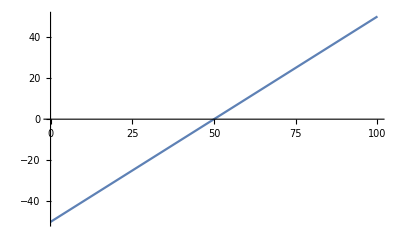

```mathematica
edge = 50
selfVertices=5
Law1[x_]:= x-edge
Law1[0]
Law1[edge] //N
Law1[2*edge] //N
Plot[Law1[x], {x, 0,2*edge}]
```

-10.

0.

10

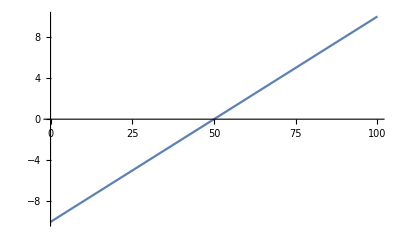

```mathematica
Law2[x_]:=Law1[x]/selfVertices
Law2[0]//N
Law2[edge] //N
Law2[2*edge]
Plot[Law2[x],{x, 0, 2*edge}]
```

-500.

-50.

0.

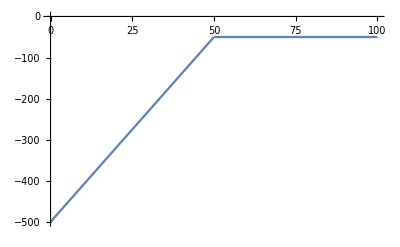

```mathematica
Law3[x_]:=Piecewise[{{-10edge+9*x, x≤edge}, {-edge, edge≤x<2*edge}, {0, x≥2*edge}}]
Law3[0]//N
Law3[edge] //N
Law3[2*edge] //N
Plot[Law3[x],{x, 0, 2*edge}]
```

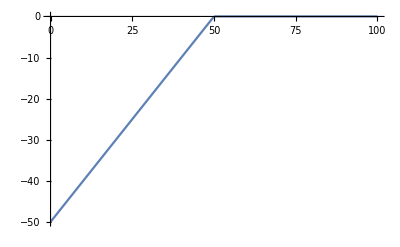

```mathematica
Law4[x_]:=Piecewise[{{x-edge, x≤edge}, {0, x>edge}}]
Plot[Law4[x],{x, 0, 2*edge}]
```